```mathematica
S[z_]:=A z^a(1-z)^b(1+c z^d)
```

```mathematica
Sgc[z_]:=5.020*10^-3 z^0.702(1-z)^1.201(1+1.952 z^4.415);
Scc[z_]:=6.483 z^2.526(1-z)^2.375(1+22.819 z^3.233);
Sccbar[z_]:=5.879*10^-4 z^0.315(1-z)^2.577(1+23.505 z^16.078);
```

```mathematica
Dc[x_]:=1/(2x)(Scc[x/2]Sccbar[x/(2-x)]+Sccbar[x/2]Scc[x/(2-x)]);
Dg[x_]:=1/(2x)(Sgc[x/2]Sgc[x/(2-x)]+Sgc[x/2]Sgc[x/(2-x)]);
```

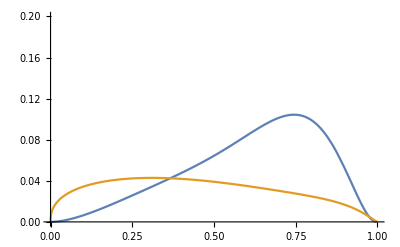

```mathematica
Plot[{Dc[x]*10^3,Dg[x]*10^4},{x,0,1},PlotRange->{{0,1},{0,0.2}}]
```